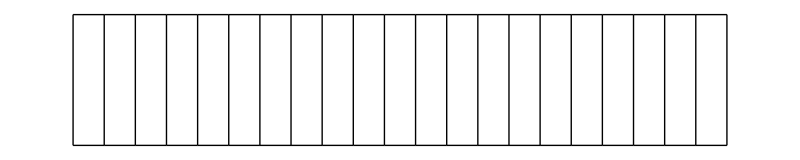
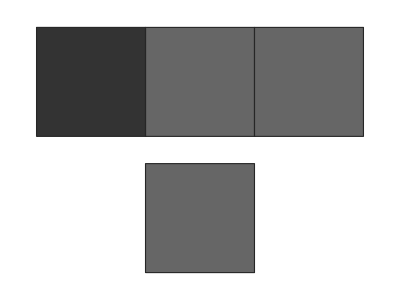
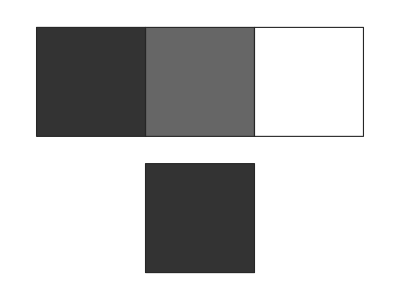
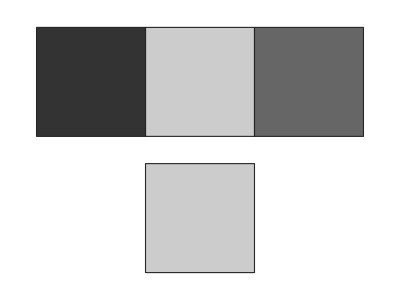
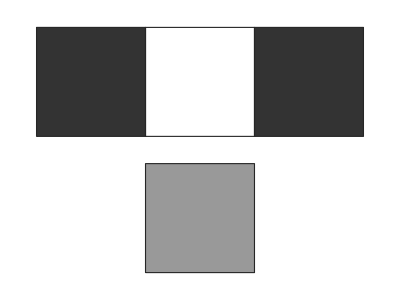
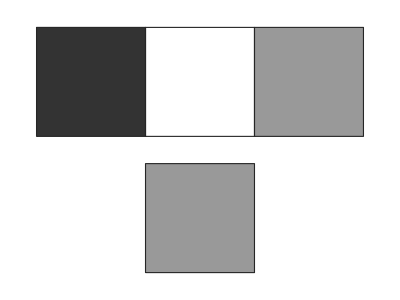
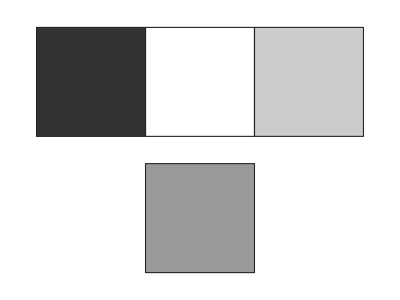
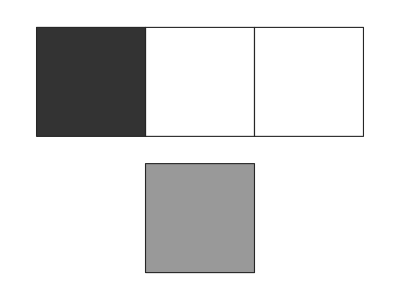

```mathematica
GraphicsRow[Graphics[With[{gfun=Function[GrayLevel[1-(#/.Verbatim[_]->0)/5]]},{EdgeForm[GrayLevel[.15]],MapIndexed[{gfun[#1],Rectangle[{#2//First,0}],Black,Text[If[#1===_,"-"],{#2//First,0}+.5]}&,#1],gfun[#2],Rectangle[{Length[#1]/2+.5,-1.25}]}],]&@@@{{4,3,3}->3,{4,3,0}->4,{4,1,3}->1,{4,0,4}->2,{4,0,2}->2,{4,0,1}->2,{4,0,0}->2,{3,3,0}->3,{2,3,0}->2,{2,1,3}->3,{2,0,_}->4,{1,3,3}->2,{1,3,0}->3,{1,1,3}->4,{1,0,3}->1,{1,0,1}->1,{1,0,0}->1,{0,3,3}->3,{0,1,3}->1,{0,1,1}->1,{_,_,_}->0},]
```